```mathematica
grid=Outer[{#1,#2}&,Range[1,10],Range[1,10]]//Flatten[#,1]&;
dd=Map[{#[[1]], #[[2]],(#[[1]]^2)/(#1[[2]])+Log[#[[2]]]}&,grid];
```

```mathematica
dd=Import[NotebookDirectory[]<>"./../R/surface.dat"][[2;;-1]]
```

{{0,2,4.8},{0,2.01,4.7},{0,2.02,4.6},{0,2.03,4.5},{0,2.04,4.5},{0,2.05,4.4},{0,2.06,4.3},{0,2.07,4.2},{0,2.08,4.2},{0,2.09,4.1},{0,2.1,4},{0,2.11,4},{0,2.12,3.9},{0,2.13,3.8},32998,{160,4.37,3.2},{160,4.38,3.2},{160,4.39,3.2},{160,4.4,3.2},{160,4.41,3.2},{160,4.42,3.2},{160,4.43,3.2},{160,4.44,3.2},{160,4.45,3.2},{160,4.46,3.3},{160,4.47,3.3},{160,4.48,3.3},{160,4.49,3.3},{160,4.5,3.3}}
 |  |  |  |

```mathematica
Clear[d,f1,f2,f3,g3]
```

```mathematica
?BSplineBasis
```

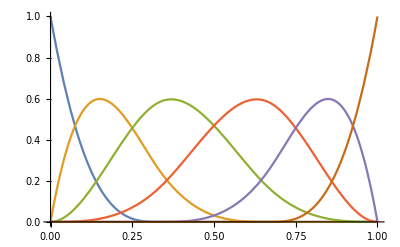

```mathematica
knots={0,0,0,0,1/3,2/3,1,1,1,1};
Plot[Evaluate[Table[BSplineBasis[{3,knots},i,x],{i,0,5}]],{x,0,1}]
```

```mathematica
f1[x_]=Sum[a[i]BSplineBasis[{3,160*knots},i,x],{i,0,5}]
f2[y_]=Sum[b[i]BSplineBasis[{3,3(1.5+knots)},i,y],{i,0,5}]
f3[z_]=Sum[c[i]BSplineBasis[{3,6 *knots},i,z],{i,0,5}]
g3[z_]=Sum[d[i]BSplineBasis[{3,6 *knots},i,z],{i,0,5}]
```

a[0] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},0,x]+a[1] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},1,x]+a[2] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},2,x]+a[3] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},3,x]+a[4] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},4,x]+a[5] BSplineBasis[{3,{0,0,0,0,160/3,320/3,160,160,160,160}},5,x]

b[0] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},0,y]+b[1] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},1,y]+b[2] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},2,y]+b[3] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},3,y]+b[4] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},4,y]+b[5] BSplineBasis[{3,{4.5,4.5,4.5,4.5,5.5,6.5,7.5,7.5,7.5,7.5}},5,y]

BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},0,z] c[0]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},1,z] c[1]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},2,z] c[2]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},3,z] c[3]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},4,z] c[4]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},5,z] c[5]

BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},0,z] d[0]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},1,z] d[1]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},2,z] d[2]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},3,z] d[3]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},4,z] d[4]+BSplineBasis[{3,{0,0,0,0,2,4,6,6,6,6}},5,z] d[5]

```mathematica
deg=5;
```

```mathematica
f1[x_]=Sum[a[i]x^i,{i,0,deg}]
f2[y_]=Sum[b[i]y^i,{i,0,deg}]
f3[z_]=Sum[c[i]z^i,{i,0,deg}]
g3[z_]=Sum[d[i]z^i,{i,0,deg}]
```

a[0]+x a[1]+x^2 a[2]+x^3 a[3]

b[0]+y b[1]+y^2 b[2]+y^3 b[3]

c[0]+z c[1]+z^2 c[2]+z^3 c[3]

d[0]+z d[1]+z^2 d[2]+z^3 d[3]

```mathematica
Join[Array[a,deg+1,{0,deg}],Array[b,deg+1,{0,deg}], Array[c,deg+1,{0,deg}],Array[d,deg+1,{0,deg}]]
```

```mathematica
eqs=Function[{x,y,z},x-f3[z]+g3[z](y-x)]@@@ddd;
```

```mathematica
res=NMinimize[Total@(eqs^2),Join[ Array[c,deg+1,{0,deg}],Array[d,deg+1,{0,deg}]], Method->"DifferentialEvolution"]
```

NMinimize::nnum: The function value Power[-0.505683 + Divide[24389 a[0], 32768] + Divide[31869 a[1], 131072] + Divide[<<2>>] + 0.524567 <<1>> + Divide[9 a[3], 65536], 2] + <<37411>> is not a number at {c[0],c[1],c[2],c[3],c[4],c[5],d[0],d[1],d[2],d[3],«2»} = {0.532215,0.278858,0.773638,0.985709,-0.221322,0.385068,0.948722,0.429215,0.562274,0.917671,«2»}.

NMinimize[1]
 |  |  |  |

```mathematica
Max[(eqs/.%[[2]])^2]
```

1.2019×10^-16

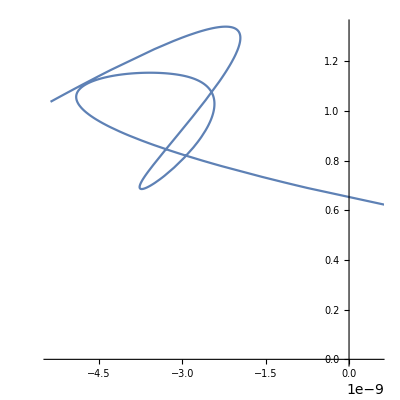

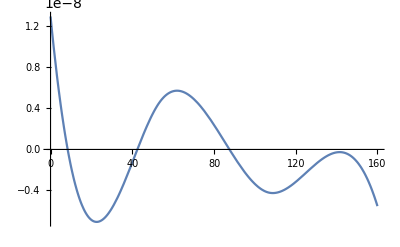

```mathematica
ParametricPlot[{f3[z],g3[z]}/.res[[2]],{z,0,6}, AspectRatio->1]
Plot[f1[x]/.res[[2]],{x,0,160}]
```

```mathematica
ListContourPlot[ddd, PlotRange->All]
ListPlot3D[ddd, PlotRange->All]
```

-Graphics-

-Graphics3D-

```mathematica
ddd=Import[NotebookDirectory[]<>"./../R/surfaceup.dat"][[2;;-1]];
```

```mathematica
wtable={{#1,#2},#3}&@@@ddd;
```

```mathematica
if=Interpolation[wtable, InterpolationOrder->1];
```

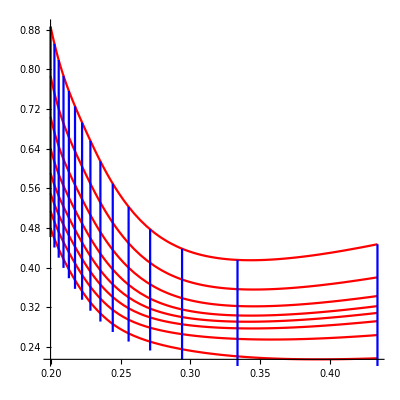

```mathematica
Show[ParametricPlot[Table[{1/Log[x],1/Log[x] if[x,y]},{y,3,4.5, .2}],{x,10,150}, AspectRatio->1, PlotStyle->Red],
ParametricPlot[Table[{1/Log[x],1/Log[x] if[x,y]},{x,10,150, 10}],{y,3,4.5}, AspectRatio->1,PlotStyle->Blue]]
```